```mathematica
ClearAll["Global`*"]
c=299792458.;
DiscreteHammingWindow[M_Integer]:=0.54-0.46 Cos[2π Range[0,M-1]/(M-1)];
ArrayResponse[θ_,d_,λ_]:=Exp[ⅈ 2π d Sin[θ]/λ];
f0=300. 10^6; (*Hz*)
λ=c/f0;
Nsnapshots=1000;
Nantennas=16;

s[t_,fs_:f0]:=Exp[2π ⅈ fs t];
snr=1.;
snapshots=Range[0,Nsnapshots-1];
Fs=10.^9;
timeSamples=snapshots/Fs;

arrayLength=(Nantennas-1) λ/2;
d[Nantennas_]:=Standardize[c/(2f0)Range[Nantennas],Mean,1&];
θ0=10.°;
a[θ_]=ArrayResponse[θ,d[Nantennas],λ];
ReceivedSignal[t_,snr_:1,θ_:θ0,fs_:f0,Nantennas_:Nantennas]:=√snr s[t,fs] ArrayResponse[θ,d[Nantennas],c/fs]+RandomVariate[NormalDistribution[],Nantennas];
y=ReceivedSignal[#,snr]&/@timeSamples;
W[θ_]=Normalize[a[θ]];
pNoisy[θ_,y_]:=Abs[W[θ]*.y]^2;
p[θ_]:=Abs[W[θ]*.a[θ0]]^2;
(*p[θ_]:=Abs[Dot[W[θ],a[θ0]]]^2;*)
b[θ_,Δ_:1°]:=1./Δ(p[θ+Δ/2.]-p[θ-Δ/2.]);
ToDecibels[x_]:=10Log10[x];
FromDecibels[y_]:=10^(y/10);

(*Plot[ToDecibels[p[θ °]],{θ,-90 ,90},PlotRange->{{-90,90},{-10,30}},Frame->{True,True,False,False},Axes->False,FrameLabel->{"Direction [°]","Power [dB]"},PlotLabel->"Beam pattern",GridLines->Automatic,ImageSize->Large];*)

Manipulate[
Plot[ToDecibels[Abs[Normalize[ArrayResponse[θ ° ,d[Nantennas],λ]*If[shouldUseWindow,DiscreteHammingWindow[Length[d[Nantennas]]],1.]]*.ArrayResponse[θ0 °,d[Nantennas],λ]]^2],{θ,-90 ,90},
PlotRange->{{-90,90},{-20,20}},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{"Direction [°]","Power [dB]"},
PlotLabel->StringForm["Noiseless beam pattern: θ_0=`1`°, M=`2`",Round[θ0],Nantennas],
GridLines->Automatic,
ImageSize->Large],
{{Nantennas,8,"M"},2,50,1},
{{θ0,0.,"θ_0"},-90 ,90},
{{shouldUseWindow,True,"Hamming window"},{True,False}}
]

(*Plot[ToDecibels[pNoisy[θ °,y[[1]]]],{θ,-90 ,90},PlotRange->{{-90,90},{-10,60}},Frame->{True,True,False,False},Axes->False,FrameLabel->{"Direction [°]","Power [dB]"},PlotLabel->"Beam pattern",GridLines->Automatic,ImageSize->Large];*)

Manipulate[
With[{y=ReceivedSignal[0.,FromDecibels[snrdB],θ0 °,f0,Nantennas]},
Plot[ToDecibels[Abs[Normalize[ArrayResponse[θ ° ,d[Nantennas],λ]]*.y]^2],{θ,-90 ,90},
PlotRange->{{-90,90},All},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{"Direction [°]","Power [dB]"},
PlotLabel->StringForm["Noisy beam pattern: θ_0=`1`°, M=`2`, SNR=`3` dB",Round[θ0],Nantennas,Round[snrdB]],
GridLines->Automatic,
ImageSize->Large]
],
{{Nantennas,8,"M"},1,50,1},
{{θ0,0.,"θ_0"},-90 ,90},
{{snrdB,10.,"SNR"},-100,100}
]

(*Plot[b[θ °],{θ,-90 ,90},PlotRange->All,FrameLabel->{"Direction [°]","Amplitude"},Frame->{True,True,False,False},Axes->False,PlotLabel->"Monopulse response",ImageSize->Large,GridLines->Automatic];*)


Manipulate[
With[{y=ReceivedSignal[0.,FromDecibels[snrdB],θ0 °,f0,Nantennas]},Plot[(Abs[Normalize[ArrayResponse[(θ+Δ/2) ° ,d[Nantennas],λ]]*.y]^2-Abs[Normalize[ArrayResponse[(θ-Δ/2) ° ,d[Nantennas],λ]]*.y]^2)/Δ,{θ,-90 ,90},
PlotRange->All,
FrameLabel->{"Direction [°]","Amplitude"},
Frame->{True,True,False,False},
Axes->False,
PlotLabel->StringForm["Monopulse response θ_0=`1`°, M=`2`, SNR=`3` dB, Δ=`4`°",Round[θ0],Nantennas,Round[snrdB],Round[Δ]],
ImageSize->Large,
GridLines->Automatic
]
],
{{Nantennas,8,"M"},1,50,1},
{{θ0,0.,"θ_0"},-90 ,90},
{{snrdB,10.,"SNR"},-100,100},
{{Δ,1.,"Phase difference"},0.1,20.}
]


StandardizedPhase[vector_]:=Standardize[Normalize/@vector,0&,First]

dPhaseOptimal[θ_]:=Norm[(IdentityMatrix[Nantennas]-1/Nantennas ConstantArray[1,{Nantennas,Nantennas}]).(Arg[y[[1]]]-Arg[a[θ]])]^2;
(*Plot[dPhase[θ °],{θ,-90,90},PlotRange->All];*)


Manipulate[
With[{y=ReceivedSignal[0.,FromDecibels[snrdB],θ0 °,f0,Nantennas]},Plot[Norm[Subtract@@StandardizedPhase/@{y,ArrayResponse[θ ° ,d[Nantennas],λ]}]^2,{θ,-90,90},
PlotRange->{{-90,90},All},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{"Direction [°]","Amplitude"},
ImageSize->Large,
GridLines->Automatic,
PlotLabel->StringForm["Phase matching: θ_0=`1`°, M=`2`, SNR=`3` dB",Round[θ0],Nantennas,Round[snrdB]]]],
{{Nantennas,8,"M"},1,50,1},
{{θ0,0.,"θ_0"},-90 ,90},
{{snrdB,10.,"SNR"},-100,100}
]

(*snrsdB=Range[0,30];
θest=Table[(θ/.Last@Quiet@FindMaximum[pNoisy[θ,ReceivedSignal[0.,FromDecibels[#],θ0 ,f0,Nantennas]],{θ,1.2θ0}]),5000]&/@snrsdB;
stdEstimate=StandardDeviation/@θest;
stdCRB=Sqrt[λ^2/(8 π^2 FromDecibels[snrsdB] Cos[θ0]^2 Total[d[Nantennas]^2])];
ListLogPlot[{{snrsdB,stdEstimate}ᵀ,{snrsdB,stdCRB}ᵀ},Joined->True]
2λ/arrayLength*)
```

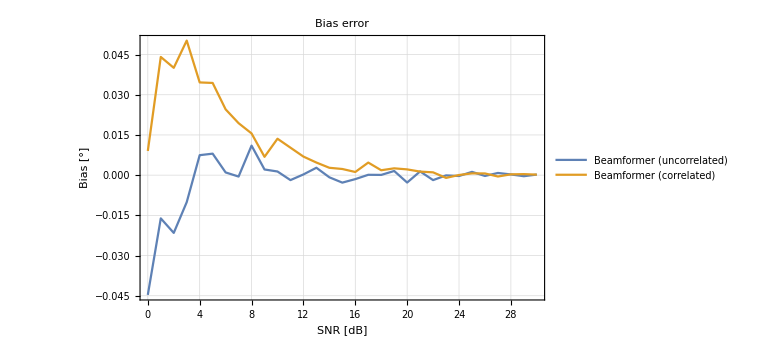

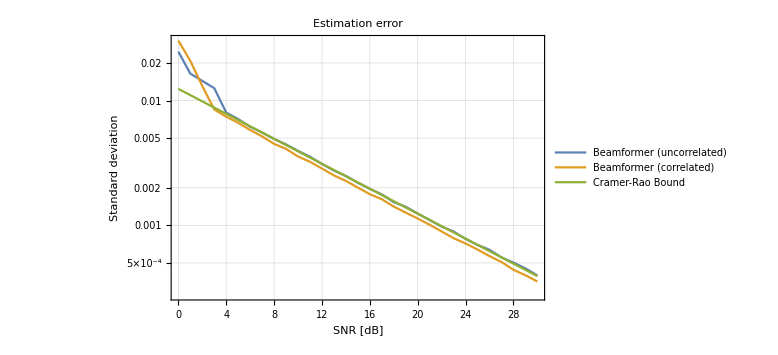

```mathematica
snrsdB=N@Range[0,30];
(*t=RandomReal[];*)
Nsimulations=5000;
MaxBeamforming[y_]:=θ/.Last@Quiet@FindMaximum[Abs[Normalize[ArrayResponse[θ  ,d[Nantennas],λ]]*.y]^2,{θ,1.2θ0},MaxIterations->10000];
(*θestimUncorr=ParallelMap[MaxBeamforming,Table[ReceivedSignal[RandomReal[],FromDecibels[#],θ0 ,f0,Nantennas],Nsimulations]&/@snrsdB,{2}];
θestimCorr=ParallelMap[MaxBeamforming,Table[ReceivedSignal[0.,FromDecibels[#],θ0 ,f0,Nantennas],Nsimulations]&/@snrsdB,{2}];*)

timesUncorr=RandomReal[{0.,1.},Nsimulations];
timesCorr=ConstantArray[0.,Nsimulations];

ysUncorr=Table[ReceivedSignal[t,FromDecibels[snr],θ0,f0,Nantennas],{snr,snrsdB},{t,timesUncorr}];
ysCorr=Table[ReceivedSignal[t,FromDecibels[snr],θ0,f0,Nantennas],{snr,snrsdB},{t,timesCorr}];

θestimUncorr=ParallelMap[MaxBeamforming,ysUncorr,{2}];
θestimCorr=ParallelMap[MaxBeamforming,ysCorr,{2}];

meanEstimateUncorr=Mean/@θestimUncorr;
meanEstimateCorr=Mean/@θestimCorr;

ListPlot[{snrsdB,(#-θ0) /Degree}ᵀ&/@{meanEstimateUncorr,meanEstimateCorr},
Joined->True,
PlotLegends->{"Beamformer (uncorrelated)","Beamformer (correlated)"},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{"SNR [dB]","Bias [°]"},
PlotLabel->"Bias error",
ImageSize->Large,
GridLines->Automatic,
PlotRange->All
]

stdEstimateUncorr=StandardDeviation/@θestimUncorr;
stdEstimateCorr=StandardDeviation/@θestimCorr;
stdCRB=Sqrt[λ^2/(8 π^2 FromDecibels[snrsdB] Cos[θ0 ]^2 Total[d[Nantennas]^2])];

ListLogPlot[{snrsdB,#}ᵀ&/@{stdEstimateUncorr,stdEstimateCorr,stdCRB},
Joined->True,
PlotLegends->{"Beamformer (uncorrelated)","Beamformer (correlated)","Cramer-Rao Bound"},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{"SNR [dB]","Standard deviation"},
PlotLabel->"Estimation error",
ImageSize->Large,
GridLines->Automatic
]
```

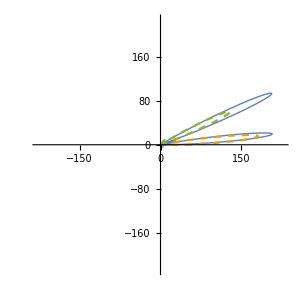

```mathematica
fs1=300. 10^6;(*Hz*)
s1[t_]:=Exp[2 π I fs1 t];
θ1=5.°;
snr1=10.;
fs2=300. 10^6;(*Hz*)
s2[t_]:=Exp[2 π I fs2 t];
θ2=25.°;
snr2=10.;

ReceivedSignal[t_,{snr1_,snr2_},{θ1_,θ2_},fs_:f0,Nantennas_:Nantennas]:=√snr1 s[t,fs] ArrayResponse[θ1,d[Nantennas],c/fs]+√snr2 s[t,fs] ArrayResponse[θ2,d[Nantennas],c/fs]+RandomVariate[NormalDistribution[],Nantennas];

y1=ReceivedSignal[#,snr1,θ1]&/@timeSamples;
y2=ReceivedSignal[#,snr2,θ2]&/@timeSamples;
y=ReceivedSignal[#,{snr1,snr2},{θ1,θ2},f0,Nantennas]&/@timeSamples;

timeSamplesRandom=RandomReal[{0.,1.},Length[timeSamples]];
yRandomTime=ReceivedSignal[#,{snr1,snr2},{θ1,θ2},f0,Nantennas]&/@timeSamplesRandom;

GraphicsRow[
{
Plot[{ToDecibels[pNoisy[θ °,First@yRandomTime]],ToDecibels[pNoisy[θ °,First@y1]],ToDecibels[pNoisy[θ °,First@y2]]},
{θ,-90,90},PlotRange->{{-90,90},{-10,30}},Frame->{True,True,False,False},PlotStyle->{{Thick},{Dashed},{Dashed}},Axes->False,FrameLabel->{"Direction [°]","Power [dB]"},PlotLabel->"Beam pattern",PlotLegends->{"y_1+y_2","y_1","y_2"},GridLines->Automatic,ImageSize->300],
PolarPlot[{pNoisy[θ ,First@y],pNoisy[θ,First@y1],pNoisy[θ,First@y2]},{θ,-90°,90°},PlotStyle->{{Thick},{Dashed},{Dashed}},PlotRange->All,ImageSize->300]
},
ImageSize->900]
```

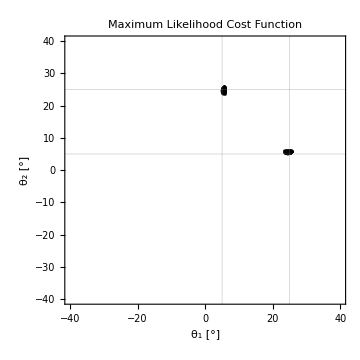

```mathematica
MaximumLikelihoodDistance2D[θ1_,θ2_,y:{_Complex..}]:=Module[{S,ΠS},S={a[θ1],a[θ2]}ᵀ;
ΠS=S.Quiet@Inverse[Sᵀ.S].Sᵀ;
Norm[y-ΠS.y]^2];
MaximumLikelihoodDistance2D[θ1_,θ2_,y:{{_Complex..}..}]:=Total[MaximumLikelihoodDistance2D[θ1,θ2,#]&/@y];

Off[Inverse::sing]
ContourPlot[Exp@Minus@MaximumLikelihoodDistance2D[θ1 °,θ2 °,First@yRandomTime],{θ1,0,40},{θ2,0,40},PlotPoints->50,ImageSize->Medium,FrameLabel->{"θ_1 [°]","θ_2 [°]"},PlotLabel->"Maximum Likelihood Cost Function",GridLines->{{θ1,θ2},{θ1,θ2}}/°,PlotRange->{{-40,40},{-40,40},All},PlotPoints->50,Contours->10^Range[-40,-10],ContourShading->False]
```

```mathematica
Off[Inverse::sing];
θ1grid=Range[0.,40.,1.];
θ2grid=Range[0.,40.,1.];
θ1θ2grid=Outer[List,θ1grid,θ2grid];
distances=Parallelize[Apply[Quiet@MaximumLikelihoodDistance2D[##,yRandomTime]&,θ1θ2grid,{2}]];
Extract[θ1θ2grid,Position[distances,Min[Cases[Flatten[distances,1],_Real]]]]
```

{{9.,31.},{31.,9.}}

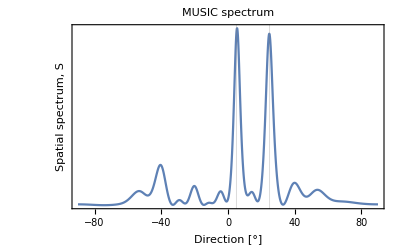

```mathematica
Un=Part[First@SingularValueDecomposition[Covariance[y]],All,3;;];
Plot[1/Norm[a[θ °]*.Un]^2,{θ,-90,90},Axes->False,GridLines->{{θ1,θ2}/Degree,Automatic},PlotRange->All,PlotLabel->"MUSIC spectrum",Frame->{True,False},FrameLabel->{"Direction [°]","Spatial spectrum, S"},FrameTicks->{{{θ1,θ2}/Degree,None},Automatic}]
```

```mathematica
MusicSpectrum[θ_,Un_]:=1/Norm[a[θ]*.Un]^2;
MusicEstimator[y_]:=Block[{Un},
Un=Part[First@SingularValueDecomposition[Covariance[y]],All,3;;];
θ/.Last@Quiet@FindMaximum[MusicSpectrum[θ,Un],{θ,#},Method->"Newton"]&/@(First/@(SortBy[FindPeaks[TimeSeries[{#,MusicSpectrum[#,Un]}&/@Range[0,π/2,0.0001]]]["Path"],Last]⟦-2;;-1⟧)/Degree)//Sort
];
MusicGridEstimator[y_]:=Block[{Un},
z=Re[y];
Un=Part[First@SingularValueDecomposition[Covariance[z]],All,3;;];
(First/@(SortBy[FindPeaks[TimeSeries[{#,MusicSpectrum[#,Un]}&/@Range[0,π/2,0.000001]]]["Path"],Last]⟦-2;;-1⟧)/Degree)//Sort
];
```

```mathematica
Nmcsimulations=101;
snapshotsRange={2,Length[y],100};
yMC=Table[ReceivedSignal[#,{snr1,snr2},{θ1,θ2},f0,Nantennas]&/@RandomReal[{0.,1.},Length[timeSamples]],Nmcsimulations];
musicEstimates=ParallelTable[MusicEstimator[y⟦;;nsnap⟧],{y,yMC},{nsnap,Range@@snapshotsRange}];
musicMeans=Map[Mean,Transpose[Map[Sort,musicEstimates,{2}],{3,2,1}],{2}];
musicStds=Map[StandardDeviation,Transpose[Map[Sort,musicEstimates,{2}],{3,2,1}],{2}];
```

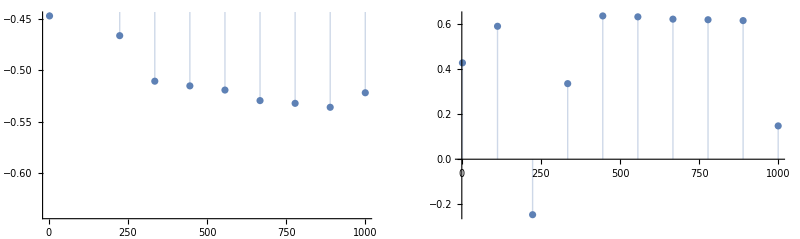

```mathematica
GraphicsRow[ListPlot[#,Joined->False,Filling->Axis,DataRange->snapshotsRange[[1;;2]]]&/@Transpose[Sort/@((#-{θ1 ,θ2 }/Degree)&/@(musicEstimates⟦1⟧))]]
```

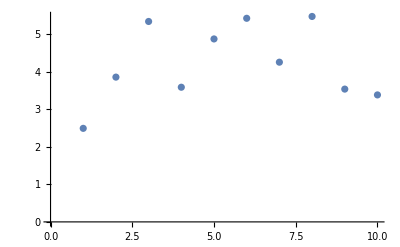
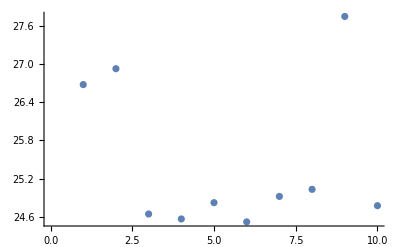

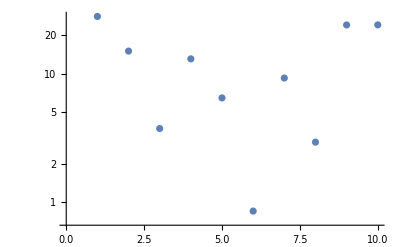
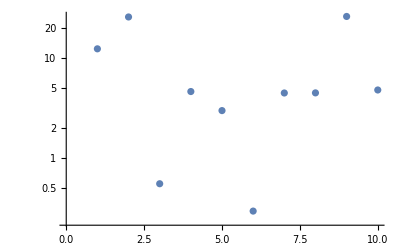

```mathematica
ListPlot/@musicMeans
ListLogPlot/@musicStds
```

```mathematica
musicEstimatesSorted=Transpose[Map[Sort,musicEstimates,{2}],{3,2,1}];
```

```mathematica
Dimensions[musicEstimatesSorted]
```

{2,10,101}

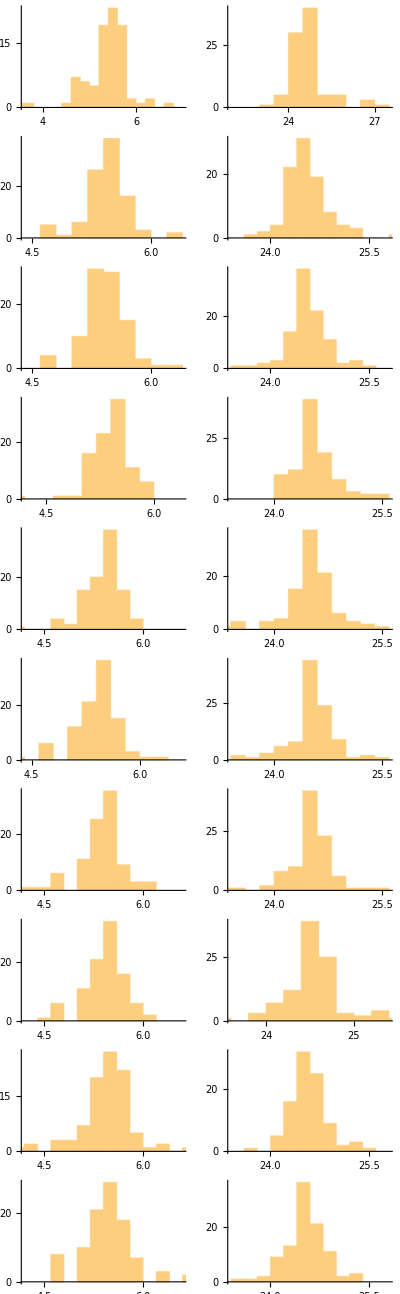

```mathematica
GraphicsGrid[Transpose[Map[Histogram,musicEstimatesSorted,{2}]],ImageSize->400]
```

```mathematica
ListPlot/@Map[Mean,musicEstimatesSorted,{2}]
```

{-Graphics-,-Graphics-}

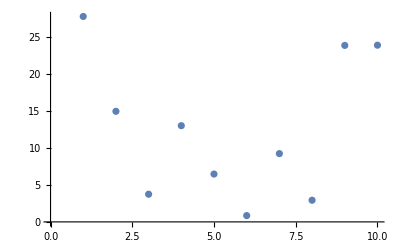
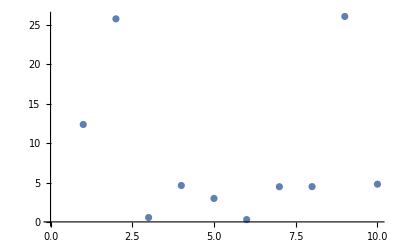

```mathematica
ListPlot/@Map[StandardDeviation,musicEstimatesSorted,{2}]
```

```mathematica
Nmcsimulations=101;
snrsdB=Range[-30,30,10];
snapshotsRange={2,Length[y],100};
timeSamplesRandom=RandomReal[{0,1},10];
yMC=Table[Table[ReceivedSignal[#,FromDecibels[{snr,snr}],{θ1,θ2},f0,Nantennas]&/@timeSamplesRandom,Nmcsimulations],{snr,snrsdB}];
```

```mathematica
musicEstimates=Transpose[ParallelMap[MusicGridEstimator,yMC,{2}],{2,3,1}];
```

Part::take: Cannot take positions -2 through -1 in {{6.×10^-6,0.0844205}}.

Sort::normal: Nonatomic expression expected at position 1 in Sort[0.000343775].

Transpose::tperm: Permutation {2,3,1} is longer than the dimensions {7,101} of the expression.

```mathematica
musicEstimates//Dimensions
```

{2,7,101}

{{5.29438,5.06928,4.62033,4.78139},{25.2291,24.6707,24.6013,24.5893}}

{{2.8772,2.22475,3.69792,1.01477},{5.35559,0.375782,0.533706,0.116697}}

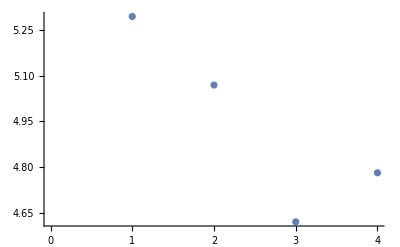
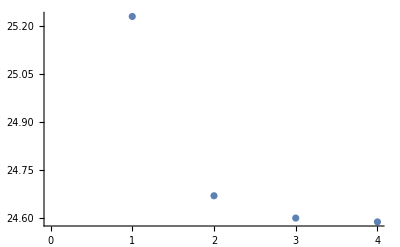

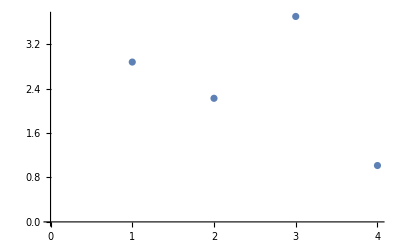
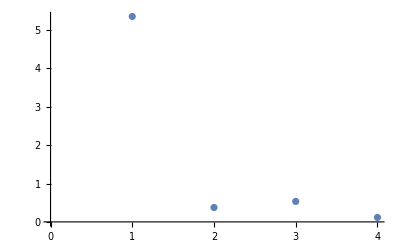

```mathematica
Map[Mean,musicEstimates,{2}]
Map[StandardDeviation,musicEstimates,{2}]
ListPlot/@Map[Mean,musicEstimates,{2}]
ListPlot/@Map[StandardDeviation,musicEstimates,{2}]
```

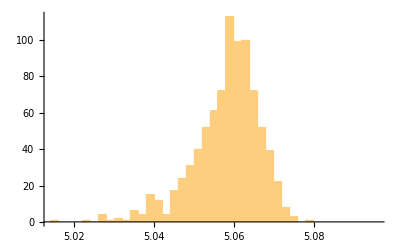
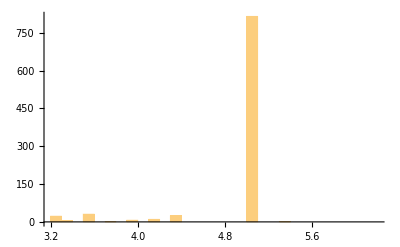
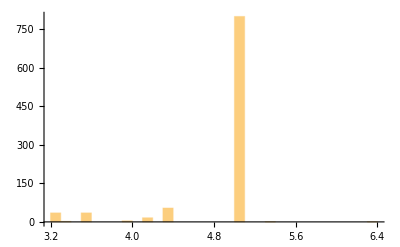
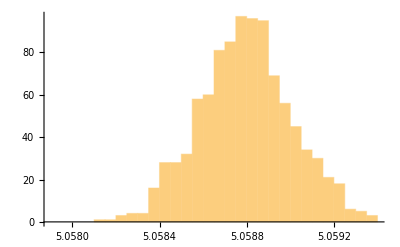
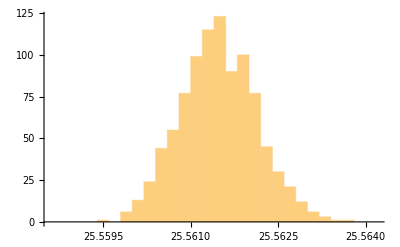
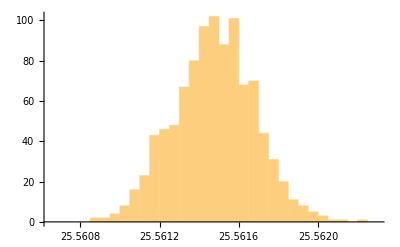
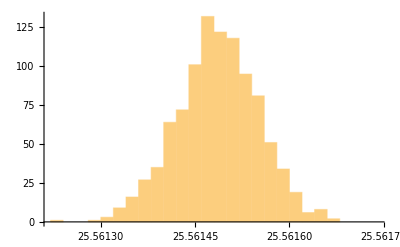
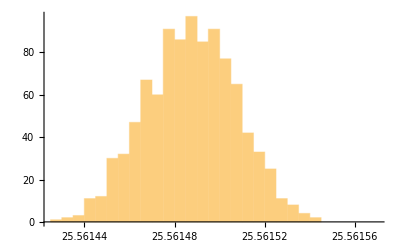

```mathematica
Map[Histogram,musicEstimates,{2}]
```

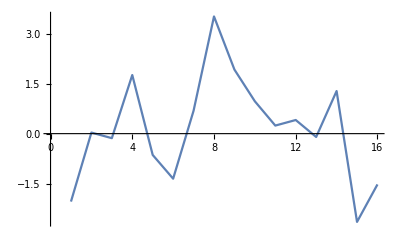

```mathematica
ListPlot[Re[yMC[[1,1,1]]],Joined->True]
```

```mathematica
FromDecibels[30]
```

1000

```mathematica
yMC//Dimensions
```

{7,1001,1000,16}

```mathematica
RandomReal[{0,1},Length[timeSamples]]
```

{0.801554,0.0496161,0.671838,0.106495,0.404108,0.320946,0.997418,0.91873,0.591707,0.095491,0.899214,0.726605,0.219315,0.0916403,0.782765,0.904209,0.303372,0.031313,0.274749,0.0812143,0.926019,0.67326,0.152806,0.423945,0.312445,0.160185,0.634104,0.85644,0.954294,0.121579,0.626605,0.501162,0.318182,0.333345,0.667187,0.449222,0.791035,0.0045504,0.455562,0.367391,0.23767,0.718005,0.646604,0.0141048,0.799959,0.540879,0.120879,0.168829,0.454553,0.014465,0.832597,0.793571,0.904965,0.856694,0.38313,0.159658,0.527657,0.830526,0.0863552,0.137331,0.292479,0.839646,0.986785,0.76674,0.217051,0.950517,0.644278,0.956813,0.088971,0.222299,0.654169,0.628456,0.273284,0.838001,0.00799176,0.750952,0.630111,0.45227,0.209962,0.456341,0.413321,0.368752,0.796149,0.0881281,0.00469125,0.112739,0.398903,0.117376,0.914865,0.738685,0.71637,0.226325,0.950674,0.541556,0.184724,0.80677,0.909446,0.347873,0.313574,0.87782,0.684047,0.932032,0.801937,0.775745,0.910636,0.390693,0.388819,0.667116,0.468857,0.889858,0.0480336,0.367371,0.306454,0.626694,0.39128,0.872233,0.918181,0.181107,0.0932152,0.697607,0.309737,0.844094,0.642255,0.600064,0.286584,0.0411429,0.871724,0.520975,0.0367796,0.718338,0.905075,0.68255,0.263124,0.610126,0.499625,0.679896,0.328997,0.416477,0.448749,0.684762,0.706902,0.960199,0.129174,0.188509,0.514108,0.321958,0.154762,0.80106,0.154667,0.28011,0.393638,0.796924,0.856671,0.0740954,0.852692,0.164858,0.840233,0.317168,0.319393,0.254738,0.747125,0.930793,0.00528602,0.943932,0.838966,0.228954,0.459294,0.747422,0.92173,0.455538,0.838424,0.929809,0.896034,0.690527,0.221994,0.797107,0.489971,0.554649,0.863151,0.969828,0.41667,0.487953,0.582203,0.998816,0.851057,0.235241,0.302355,0.344948,0.484214,0.738306,0.615192,0.540357,0.14848,0.206365,0.764753,0.928866,0.410943,0.637734,0.689216,0.920039,0.712363,0.559801,0.190321,0.173767,0.89551,0.301297,0.277096,0.953706,0.765519,0.154266,0.271065,0.323803,0.362333,0.405394,0.688478,0.713126,0.00631612,0.335421,0.606764,0.497136,0.868534,0.764139,0.226473,0.404378,0.625623,0.514855,0.844456,0.121431,0.305303,0.96156,0.119799,0.786784,0.390721,0.429816,0.277567,0.241213,0.927741,0.540356,0.470652,0.760757,0.238751,0.500693,0.343413,0.0135501,0.963237,0.414052,0.474276,0.241892,0.348195,0.916022,0.211272,0.339067,0.8684,0.498359,0.740068,0.846735,0.749606,0.875394,0.0843693,0.41132,0.454909,0.989913,0.881952,0.532467,0.306383,0.762321,0.139939,0.584099,0.399706,0.373082,0.682075,0.53562,0.780471,0.747233,0.296515,0.483037,0.317926,0.533246,0.369003,0.171956,0.553541,0.552077,0.44064,0.275565,0.289753,0.375182,0.393617,0.178375,0.951808,0.295601,0.203938,0.762886,0.93118,0.204469,0.945655,0.642908,0.59007,0.0582365,0.304795,0.853654,0.829268,0.0612177,0.328172,0.0660924,0.359987,0.638244,0.739089,0.107802,0.499907,0.489734,0.295594,0.74743,0.516087,0.474035,0.306443,0.190773,0.392664,0.471048,0.919683,0.234796,0.601402,0.084105,0.417443,0.776658,0.71248,0.441663,0.476691,0.956014,0.22862,0.0071968,0.138998,0.18028,0.996405,0.543133,0.150397,0.759938,0.463455,0.0106295,0.715144,0.614435,0.792075,0.720881,0.947002,0.0193787,0.0205329,0.24582,0.495077,0.0476832,0.163271,0.00274801,0.152465,0.689037,0.307782,0.293013,0.0232578,0.545674,0.0863536,0.184971,0.481515,0.958047,0.545423,0.00813184,0.565964,0.941235,0.0109238,0.033254,0.338734,0.0805719,0.245156,0.90791,0.967091,0.723426,0.665509,0.0772802,0.295652,0.248008,0.129026,0.981207,0.142197,0.00301004,0.836481,0.294759,0.333089,0.752928,0.0400365,0.0185867,0.894404,0.704842,0.224084,0.427439,0.730378,0.773529,0.118346,0.61339,0.225112,0.88896,0.691967,0.23462,0.91659,0.491235,0.731042,0.375908,0.156522,0.748118,0.774513,0.144529,0.877874,0.326847,0.315896,0.712867,0.531763,0.483992,0.232743,0.581855,0.833659,0.502678,0.774553,0.341755,0.302089,0.178787,0.967369,0.788152,0.881799,0.411317,0.651214,0.846994,0.248027,0.56018,0.189007,0.384678,0.885392,0.440995,0.532632,0.061303,0.549537,0.333086,0.847971,0.386855,0.38293,0.995923,0.564023,0.370774,0.8958,0.545514,0.0641058,0.667794,0.459946,0.471715,0.256605,0.56168,0.00793367,0.567527,0.866131,0.240511,0.397836,0.562882,0.0319207,0.986688,0.956844,0.161506,0.927497,0.483269,0.523902,0.919924,0.979357,0.567622,0.46482,0.561974,0.181508,0.681779,0.517278,0.21521,0.500104,0.428549,0.243398,0.360914,0.213761,0.847445,0.527417,0.719206,0.321952,0.127502,0.635184,0.472762,0.388307,0.430321,0.896598,0.773554,0.277725,0.646854,0.540615,0.058895,0.310839,0.391023,0.893993,0.023639,0.204171,0.669525,0.257259,0.657239,0.471066,0.0257361,0.422827,0.600121,0.589575,0.740535,0.733037,0.0313377,0.0133967,0.529878,0.971157,0.146886,0.985426,0.566023,0.779153,0.177526,0.620493,0.0797716,0.591695,0.232582,0.545635,0.307903,0.290184,0.524762,0.988609,0.296775,0.949995,0.791997,0.749146,0.397618,0.140605,0.308204,0.160711,0.771467,0.619713,0.101302,0.974967,0.50963,0.105504,0.516043,0.540544,0.666163,0.496731,0.881858,0.897992,0.317744,0.395887,0.978558,0.0178061,0.514305,0.512159,0.840404,0.908477,0.691202,0.287777,0.51755,0.778099,0.638521,0.025775,0.742302,0.681669,0.321109,0.346417,0.646215,0.387894,0.613349,0.236288,0.853078,0.445268,0.788686,0.485573,0.0756442,0.184804,0.349237,0.107811,0.74858,0.391882,0.287875,0.908438,0.436063,0.349522,0.586923,0.326352,0.0246775,0.981297,0.300929,0.999699,0.940742,0.967666,0.121124,0.601559,0.737977,0.316759,0.0672395,0.1456,0.468277,0.496011,0.120387,0.92329,0.95366,0.350088,0.54841,0.485726,0.153358,0.990586,0.788182,0.367971,0.760874,0.483473,0.424423,0.686789,0.0289635,0.655362,0.130184,0.0134146,0.559111,0.594133,0.763883,0.285069,0.712076,0.541312,0.68512,0.890669,0.275225,0.777111,0.640022,0.0654106,0.251536,0.277596,0.498281,0.463852,0.972498,0.468504,0.828368,0.374449,0.144899,0.17976,0.382557,0.861919,0.680886,0.21603,0.0449983,0.566892,0.76384,0.64246,0.73571,0.781598,0.417775,0.436116,0.250358,0.674222,0.488573,0.255539,0.0863648,0.822849,0.180408,0.888272,0.651912,0.872674,0.378568,0.653932,0.797256,0.712898,0.130787,0.949593,0.0372879,0.66924,0.841282,0.19634,0.5316,0.945232,0.173456,0.880369,0.890676,0.347888,0.302206,0.0627468,0.00544662,0.0398606,0.0513717,0.987774,0.0572505,0.359857,0.382533,0.583947,0.470114,0.107867,0.569326,0.716749,0.473948,0.394035,0.949493,0.0147102,0.456886,0.341795,0.099993,0.00984999,0.907376,0.0950564,0.244707,0.476244,0.976891,0.693196,0.534092,0.139057,0.975649,0.432284,0.592376,0.673565,0.957272,0.578242,0.457617,0.487815,0.779552,0.343338,0.165815,0.415389,0.63639,0.657304,0.879129,0.66148,0.325061,0.331478,0.559585,0.0363435,0.165524,0.59153,0.262968,0.52909,0.936186,0.436393,0.640885,0.93179,0.0359274,0.460641,0.697198,0.929691,0.473993,0.860959,0.964319,0.0846949,0.129219,0.976916,0.284668,0.865421,0.30864,0.887956,0.265906,0.23508,0.621029,0.677318,0.336564,0.277528,0.645491,0.905104,0.24978,0.150148,0.886043,0.652168,0.13548,0.880627,0.813658,0.35161,0.649462,0.640297,0.870839,0.430559,0.106682,0.278964,0.174848,0.614608,0.620434,0.981442,0.868163,0.544638,0.518945,0.92637,0.490044,0.764586,0.827744,0.0913353,0.0926338,0.023816,0.141674,0.518337,0.0183623,0.52312,0.993653,0.677115,0.651179,0.599049,0.959486,0.541255,0.0308312,0.667613,0.594708,0.628198,0.239805,0.957522,0.0595119,0.987785,0.117082,0.626895,0.118658,0.750327,0.16363,0.431928,0.453479,0.568706,0.529403,0.195758,0.11542,0.86856,0.90887,0.606789,0.0466885,0.667332,0.978237,0.185785,0.496887,0.514885,0.458651,0.268721,0.961157,0.572397,0.814531,0.718694,0.800393,0.4626,0.288123,0.703814,0.108467,0.920294,0.617208,0.290417,0.229311,0.46099,0.969089,0.769234,0.905863,0.430902,0.544725,0.0137882,0.077199,0.132381,0.134807,0.70812,0.931613,0.376683,0.431985,0.190227,0.458486,0.0365928,0.576266,0.62537,0.475798,0.144031,0.846367,0.28502,0.115628,0.697538,0.323994,0.773931,0.198941,0.890635,0.938509,0.597864,0.558085,0.0506489,0.041005,0.757487,0.0451647,0.61673,0.956487,0.230661,0.436464,0.964121,0.34713,0.827027,0.934998,0.532635,0.114986,0.350418,0.671119,0.975407,0.530622,0.962681,0.641778,0.305662,0.696815,0.742021,0.758932,0.908432,0.79664,0.551674,0.539628,0.0884002,0.735686,0.982398,0.185221,0.648381,0.751038,0.949316,0.0513511,0.567053,0.53083,0.594978,0.349851,0.724397,0.406677,0.738616,0.92352,0.922712,0.337404,0.481926,0.588651,0.0157461,0.474563,0.918862,0.954992,0.378517,0.0826769,0.705636,0.818711,0.299415,0.97051,0.182636,0.448608,0.469906,0.44037,0.444986,0.00774195,0.523636,0.369174,0.799545,0.088943,0.938117,0.534785,0.251111,0.669514,0.0243761,0.152067,0.514094,0.799873,0.858815,0.826083,0.5834,0.0177533,0.144087,0.236219,0.475532,0.547121,0.526819,0.505781,0.0160715,0.453041,0.420537,0.27796,0.146393,0.716205,0.680817,0.165356,0.938174,0.292071,0.66842,0.685345,0.00567723,0.972095,0.47098,0.378945,0.829689,0.44839,0.259516,0.95485,0.807982,0.193897,0.186543,0.975658,0.453104,0.0108597,0.875846,0.967354,0.154761,0.768116,0.495027,0.984389,0.497474,0.623686,0.526882,0.347524,0.820124,0.235026,0.882515,0.88673,0.194873,0.207191,0.242383,0.700471,0.715929,0.918694}